```mathematica
space = Table[0,{20},{20}];
```

```mathematica
space2= Table[0,{20},{20}];
```

```mathematica
universe=Table[0,{50},{50}];
universeBackup=Table[0,{50},{50}];
```

```mathematica
visualUniverse=Table[0,{50},{50}];
```

```mathematica
ArrayPlot[space]
```

-Graphics-

```mathematica
tiles={{{0,1,1,1,1,1,1,1},{0,0,1,0,1,0,0,0},{1,0,1,0,0,0,0,0},{1,1,1,1,0,0,0,0}},{{1,0,0,1},{1,1,1,1},{0,1,1,0},{0,1,1,0},{1,1,1,1},{1,0,0,1}},{{1,1,1,1,0,0,1,1,1,1,1,1,1},{1,0,1,0,0,0,0,1,1,0,0,0,0},{0,0,1,0,1,1,0,1,1,1,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0}}}
```

{{{0,1,1,1,1,1,1,1},{0,0,1,0,1,0,0,0},{1,0,1,0,0,0,0,0},{1,1,1,1,0,0,0,0}},{{1,0,0,1},{1,1,1,1},{0,1,1,0},{0,1,1,0},{1,1,1,1},{1,0,0,1}},{{1,1,1,1,0,0,1,1,1,1,1,1,1},{1,0,1,0,0,0,0,1,1,0,0,0,0},{0,0,1,0,1,1,0,1,1,1,0,0,0},{0,1,1,1,1,1,1,1,0,1,0,0,0}}}

```mathematica
tiles=Flatten[allTiles/@tiles,1];
```

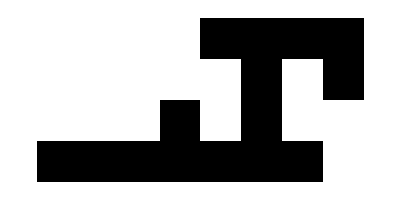
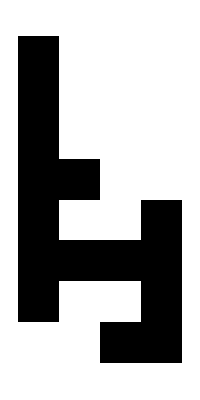
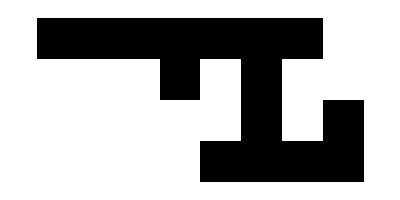
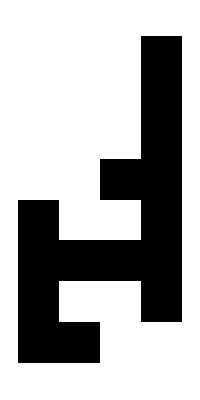
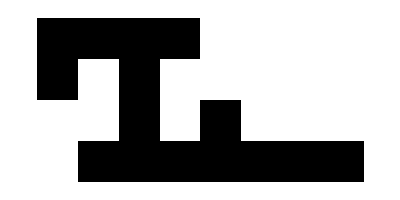
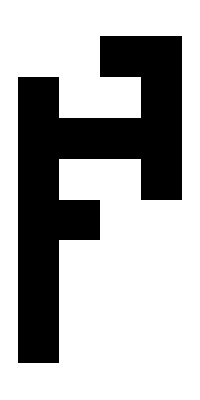
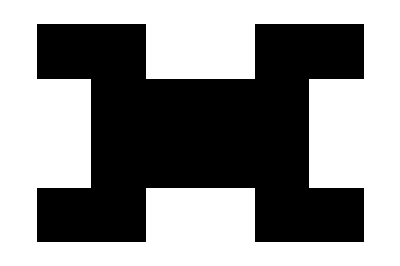
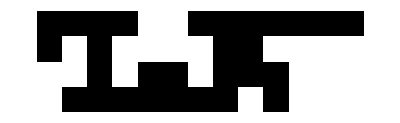
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@tiles
```

```mathematica
tile={{1,1,1},{1,0,0}}
```

{{1,1,1},{1,0,0}}

```mathematica
space=addTile[tiles[[1]],space,{1,1}];
visualSpace=(RandomReal[]*0.9+0.1)*space;
```

```mathematica
space2=addTile[tiles[[1]],space2,{1,1}];
```

```mathematica
ArrayPlot[space]
```

-Graphics-

```mathematica
putUniverse[universe,space,{1,1}]
```

-Graphics-

```mathematica
visualUniverse=visualUniverse+(RandomReal[])*(universe-universeBackup);
```

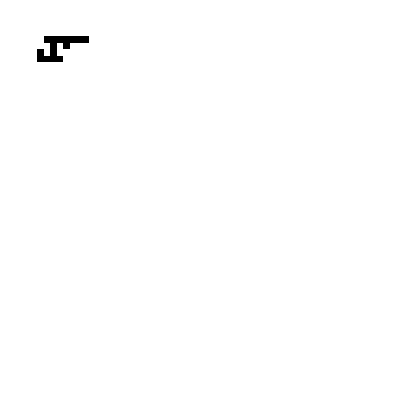

```mathematica
ArrayPlot[visualUniverse]
```

```mathematica
mirrorv[tile_]:=Module[{line={},tMirror={}},
tMirror={};
For[i=1,i≤Length[tile],i++,
line={};
For[j=Length[tile[[1]]],j≥1,j--,
AppendTo[line,tile[[i,j]]];
];
AppendTo[tMirror,line];
];
tMirror
]
```

```mathematica
rotatec[tile_]:=Module[{line={},tMirror={}},
tMirror={};
For[i=1,i≤Length[tile[[1]]],i++,
line={};
For[j=Length[tile],j≥1,j--,
AppendTo[line,tile[[j,i]]];
];
AppendTo[tMirror,line];
];
tMirror
]
```

```mathematica
allTiles[tile_]:=Module[{list={}},
list=Join[NestList[rotatec,tile,3],
NestList[rotatec,mirrorv[tile],3]];
list=DeleteDuplicates[list];
list
]
```

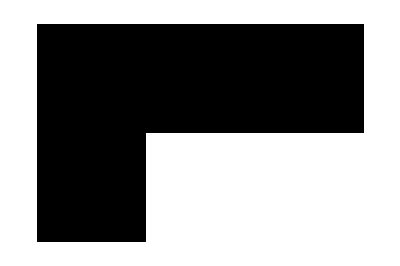
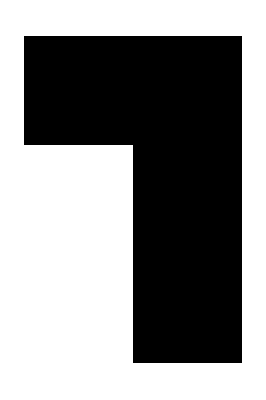
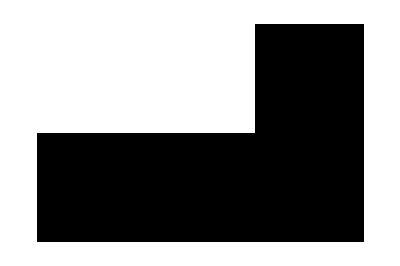
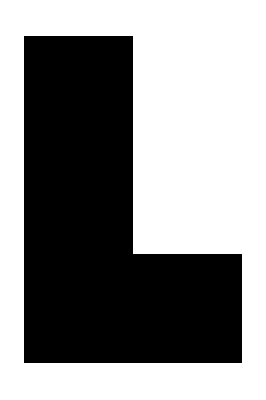
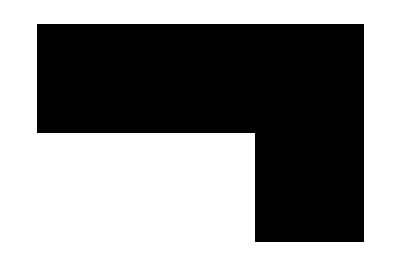
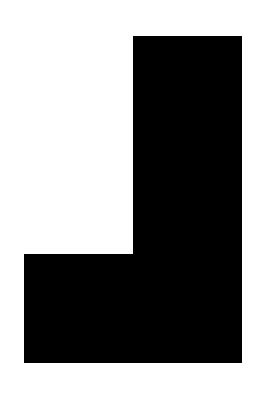
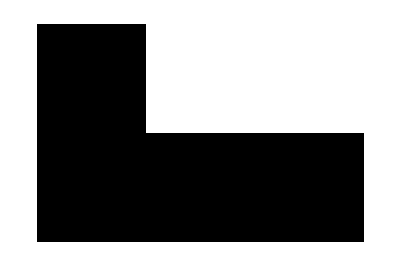
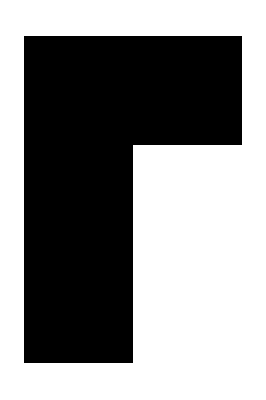

```mathematica
Map[ArrayPlot[#,Frame->False]&,allTiles[tile]]
```

```mathematica
positionTile[tile_,{x_,y_},{w_,h_}]:=Module[{temptile,addrowsa,addrowsb},
temptile=MapThread[Join,{Table[0,{Dimensions[tile][[1]]},{x-1}],tile,Table[0,{Dimensions[tile][[1]]},{w-(x-1+Dimensions[tile][[2]])}]
}
];
addrowsa=Table[0,{y-1},{w}];
addrowsb=Table[0,{h-(y-1+Dimensions[tile][[1]])},{w}];
Join[addrowsa,temptile,addrowsb]
]
```

```mathematica
increaseSpace[space_,d_,l_]:=Module[{newSpace},
If[d==1,
addrows=Table[0,{l},{Dimensions[space][[2]]}];
newSpace=Join[addrows,space];
];
If[d==3,
addrows=Table[0,{l},{Dimensions[space][[2]]}];
newSpace=Join[space,addrows];
];
If[d==2,
newSpace=MapThread[Join,{space,Table[0,{Dimensions[space][[1]]},{l}]}];
];
If[d==4,
newSpace=MapThread[Join,{Table[0,{Dimensions[space][[1]]},{l}],space}];
];
newSpace
]
```

```mathematica
growSpace[space_,l_]:=Module[{},
Fold[increaseSpace[#1,#2,1]&,{space,1,2,3,4}]
]
```

```mathematica
overlapQ[tile_,space_,{x_,y_}]:=Module[{delta},
delta=positionTile[tile,{x,y},Dimensions[space]];
Max[delta+space]!=1
]
```

```mathematica
detectVoid[space_]:=Module[{},
selectedRegion=usedSpace[space];
(*img=Image[selectedRegion,"Bit"];*)
(*IntegerPart[Max[ImageData[FillingTransform[img,Padding->0,CornerNeighbors->True]-img]]]*)
(*IntegerPart[Max[Union[Flatten[ImageData@FillingTransform[img,CornerNeighbors->True]-ImageData@img]]]]*)
!(Values@ComponentMeasurements[selectedRegion,"Count"]==Values@ComponentMeasurements[selectedRegion,"FilledCount"])
]
```

```mathematica
usedRange[space_]:={MinMax[Last/@Position[space,1]],MinMax[First/@Position[space,1]]}
```

```mathematica
score[space_]:=Module[{},
If[space==0, Return[Infinity];];
If[TrueQ[detectVoid[space]],Infinity,
{xRange,yRange}=usedRange[space];
First[(Differences[xRange]+1)*(Differences[yRange]+1)]
]
]
```

```mathematica
addTile[tile_,space_,{x_,y_}]:=Module[{},
If[overlapQ[tile,space,{x,y}]==True,0,
space+positionTile[tile,{x,y},Dimensions[space]]
]
]
```

```mathematica
scanRange[tile_,space_]:=Module[{},
xRange=usedRange[space][[1]];
yRange=usedRange[space][[2]];
{h,w}=Dimensions[tile];
{hMax,wMax}=Dimensions[space];
{{Max[xRange[[1]]-w,1],Min[xRange[[2]]+1,wMax-w+1]},{Max[yRange[[1]]-h,1],Min[yRange[[2]]+1,hMax-h+1]}}
]
```

```mathematica
scoreImg[space_]:=Max[1-ImageData[Blur[Downsample[Rasterize[ArrayPlot[space]],5,5],20]]]
```

```mathematica
innerBound[region_]:=Module[{n},
(*n=1;
While[Length[Union[Flatten[Drop[Drop[Map[Drop[Drop[#,n],-n]&,usedSpace[region]],n],-n]]]]>1,
If[2*(n+1)>Min[Dimensions[usedSpace[region]]],
n++;
Break[];
];
n++];
n*)
Max[Map[distanceFromBoundary[#,Dimensions[usedSpace[universe]]]&,Position[usedSpace[universe],0]]]
]
```

```mathematica
usedSpace[space_]:=Module[{xRange,yRange,selectedRows},
xRange=MinMax[Last/@Position[space,1]];
yRange=MinMax[First/@Position[space,1]];
selectedRows=Take[space,yRange];
Map[Take[#,xRange]&,selectedRows]
]
```

```mathematica
overlay[space_,{{xmin_,xmax_},{ymin_,ymax_}}]:=Module[{},
temptile=Table[2,{y,ymin,ymax},{x,xmin,xmax}];
ArrayPlot[space+positionTile[temptile,{xmin,ymin},Dimensions[space]]]
]
```

```mathematica
addNextTile[space_,tiles_]:=(
SetSharedVariable[minScores];
minScores={};
ParallelMap[
tile=#;
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[Join[scores,{1}],_Integer]]*(1-scoresImg);
newPos=Reverse[First[Take[Position[scores,Min[scores]],1]]]+First/@regiontoscan-{1,1};
AppendTo[minScores,{Min[scores],addTile[tile,space,newPos]}];
&,tiles];
First[SortBy[minScores,#[[1]]&]][[2]]
)
```

```mathematica
addNextTilewCost[space_,tiles_]:=(
SetSharedVariable[minScores];
minScores={};
ParallelMap[
tile=#;
regiontoscan=scanRange[tile,space];
scores=Transpose[Table[score[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scoresImg=Transpose[Table[scoreImg[addTile[tile,space,{x,y}]],{x,regiontoscan[[1,1]],regiontoscan[[1,2]]},{y,regiontoscan[[2,1]],regiontoscan[[2,2]]}]];
scores=scores/Max[Cases[Join[scores,{1}],_Integer]]*(1-scoresImg);
newPos=Reverse[First[Take[Position[scores,Min[scores]],1]]]+First/@regiontoscan-{1,1};
AppendTo[minScores,{Min[scores],addTile[tile,space,newPos]}];
&,tiles];
First[SortBy[minScores,#[[1]]&]]
)
```

```mathematica
putUniverse[universe_,space_,{offsetx_,offsety_}]:=Module[{},
For[j=offsety,j≤ offsety+Dimensions[space][[1]]-1,j++,
universe[[j]][[offsetx;;(offsetx+Dimensions[space][[2]]-1)]]=space[[j-offsety+1]];
];
universe//ArrayPlot
]
SetAttributes[putUniverse,HoldFirst];
```

```mathematica
takeUniverse[universe_,{offsetx_,offsety_},{width_,height_}]:=Module[{xRange,yRange,selectedRows},
xRange={offsetx,offsetx+width-1};
yRange={offsety,offsety+height-1};
selectedRows=Take[universe,yRange];
Map[Take[#,xRange]&,selectedRows]
]
```

```mathematica
growDownStep[universe_,tiles_,offsetx_,visualUniverse_]:=Module[{},
universeBackup=universe;
visualUniverseBackup=visualUniverse;
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
usedrange=usedRange[universe];
ibound=innerBound[universe];
spaced=takeUniverse[universe,{offsetx,usedrange[[2,2]]-ibound},{dimension,dimension}];
spaced=addNextTile[spaced,tiles];
putUniverse[universe,spaced,{offsetx,usedrange[[2,2]]-ibound}];
visualUniverse=visualUniverse+RandomReal[]*(universe-universeBackup);
ArrayPlot[visualUniverse]
]
```

```mathematica
showUniverse[universe_,tiles_,{offsetx_,offsety_},visualUniverse_]:=Module[{},
universeBackup=universe;
visualUniverseBackup=visualUniverse;
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
usedrange=usedRange[universe];
ibound=innerBound[universe];
spaced=takeUniverse[universe,{offsetx,offsety},{dimension,dimension}]
(*spaced=addNextTile[spaced,tiles];
putUniverse[universe,spaced,{offsetx,offsety}];
visualUniverse=visualUniverse+RandomReal[]*(universe-universeBackup);
ArrayPlot[visualUniverse]*)
]
```

```mathematica
growUniverse[universe_,tiles_,{offsetx_,offsety_},visualUniverse_]:=Module[{},
universeBackup=universe;
visualUniverseBackup=visualUniverse;
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
usedrange=usedRange[universe];
ibound=innerBound[universe];
spaced=takeUniverse[universe,{offsetx,offsety},{dimension,dimension}];
spaced=addNextTile[spaced,tiles];
putUniverse[universe,spaced,{offsetx,offsety}];
visualUniverse=visualUniverse+RandomReal[]*(universe-universeBackup);
ArrayPlot[visualUniverse]
]
trygrowUniverse[universe_,tiles_,{offsetx_,offsety_}]:=Module[{},
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
usedrange=usedRange[universe];
ibound=innerBound[universe];
spaced=takeUniverse[universe,{offsetx,offsety},{dimension,dimension}];
addNextTilewCost[spaced,tiles]
]
```

```mathematica
SetAttributes[growUniverse,HoldAll]
```

```mathematica
SetAttributes[growDownStep,HoldAll]
```

```mathematica
growSideStep[universe_,tiles_,offsety_,visualUniverse_]:=Module[{},
universeBackup=universe;
visualUniverseBackup=visualUniverse;
dimension=Ceiling[1.5*(First/@Dimensions/@tiles//Max)];
usedrange=usedRange[universe];
ibound=innerBound[universe];
spaced=takeUniverse[universe,{usedrange[[1,2]]-ibound,offsety},{dimension,dimension}];
spaced=addNextTile[spaced,tiles];
putUniverse[universe,spaced,{usedrange[[1,2]]-ibound,offsety}];
visualUniverse=visualUniverse+RandomReal[]*(universe-universeBackup);ArrayPlot[visualUniverse]
]
```

```mathematica
SetAttributes[growSideStep,HoldAll]
```

```mathematica
distanceFromBoundary[point_,dimension_]:=Module[{x,y},
x=0;
y=0;
If[point[[1]]≥dimension[[1]]/2,
x=dimension[[1]]-point[[1]];,
x=point[[1]];
];
If[point[[2]]≥dimension[[2]]/2,
x=dimension[[2]]-point[[2]];,
x=point[[2]];
];
Max[x,y]
];
```

```mathematica
addNextTileLocal[]:=(
space2=space;
visualSpace2=visualSpace;
space=addNextTile[space,tiles];
visualSpace=visualSpace+RandomReal[]*(space-space2);
ArrayPlot[visualSpace]
)
```

```mathematica
switchToUniversal[]:=(
putUniverse[universe,space,{1,1}];
putUniverse[visualUniverse,visualSpace,{1,1}];
)
```

```mathematica
findPerimeter[region_]:=Position[Erosion[region,1]-Erosion[region,2],1]
```

```mathematica
growUniverse[universe_,tiles_,visualUniverse_]:=Module[{},
universeBackup=universe;
SetSharedVariable[minMinScores];
minMinScores={};
Map[
offset=#;
AppendTo[minMinScores,trygrowUniverse[universe,tiles,offset]];
&,
Position[Erosion[universe,1]-Erosion[universe,2],1]
];
universe=First[SortBy[minMinScores,#[[1]]&]][[2]];
visualUniverse=visualUniverse+RandomReal[]*(universe-universeBackup);
]
```

```mathematica
SetAttributes[growUniverse,HoldAll]
```